# Monetary Policy

## Setup

Set working directory

```mathematica
SetDirectory["/Users/nicoloceneda/Dropbox/Bhamra-Ceneda/theory/macroeconomics/code"];
```

## Consumption and Investment

## Maximum Safe to Spend

Clear variables

```mathematica
Clear["Global`*"]
```

Maximum safe to spend

```mathematica
maxC[μ_,T_]:=(μ *w0)/((1+μ)-(1+μ)^(1-T))
```

Maximum safe to spend when μ = 0

```mathematica
Limit[(w0*μ)/((1+μ)-(1+μ)^(1-T)),μ->0]
```

w0/T

Household wealth

```mathematica
w[μ_,t_,T_]:=w0*(1+μ)^t-maxC[μ,T]*(1+μ)*((1+μ)^t-1)/μ
```

Parameters

```mathematica
w0=1;
```

Plot household maximum safe to spend and wealth

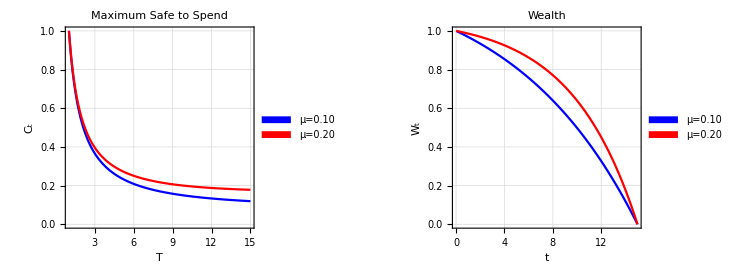

```mathematica
householdConsumption= Plot[{maxC[0.10,T],maxC[0.20,T]},{T,1,15},
PlotStyle->{Blue,Red},
PlotLabel->"Maximum Safe to Spend",
PlotLegends->Placed[SwatchLegend[{"μ=0.10","μ=0.20"}],{0.87,0.88}],
FrameLabel->{"T","C_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{1,15},{0,1}}];
householdWealth= Plot[{w[0.10,t,15],w[0.20,t,15]},{t,0.01,15},
PlotStyle->{Blue,Red},
PlotLabel->"Wealth",
PlotLegends->Placed[SwatchLegend[{"μ=0.10","μ=0.20"}],{0.87,0.88}],
FrameLabel->{"t","W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,15},{0,1}}];
householdWealth=GraphicsGrid[{{householdConsumption,householdWealth}},ImageSize->{750,270}]
Export["images/household-wealth.jpeg",householdWealth];
```

## Static Optimal Control Problem in Discrete Time

Household utility

```mathematica
u[c_,η_]:=(c^(1-η)-1)/(1-η)
```

Plot household utility

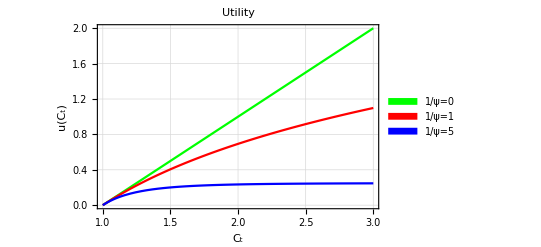

```mathematica
householdUtility=Plot[{u[c,0],Log[c],u[c,5]},{c,1,3},
PlotStyle->{Green,Red,Blue},
PlotLabel->"Utility",
PlotLegends->Placed[SwatchLegend[{"1/ψ=0","1/ψ=1","1/ψ=5"}],{0.12,0.75}],
FrameLabel->{"C_t","u(C_t)"},
Frame->True,
GridLines->Automatic,
PlotRange->{{1,3},{0,2}}]
Export["images/household-utility.jpeg",householdUtility];
```

Clear variables

```mathematica
Clear["Global`*"]
```

Optimal consumption-wealth ratio

```mathematica
optimalCW[β_,ψ_,μ_]:=(1+μ)^(1-ψ)/((1+μ)^(1-ψ)+β^ψ)
```

Plot optimal savings-wealth ratio and consumption-wealth ratio

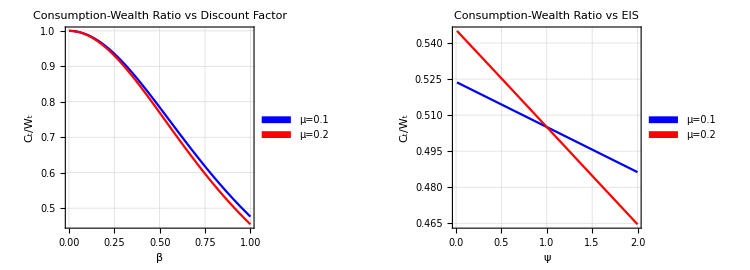

```mathematica
consumptionWealthBeta=Plot[{optimalCW[β,2,0.1],optimalCW[β,2,0.2]},{β,0,1},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Wealth Ratio vs Discount Factor",
PlotLegends->Placed[SwatchLegend[{"μ=0.1","μ=0.2"}],{0.87,0.88}],
FrameLabel->{"β","C_t/W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,1},{Min[optimalCW[1,2,0.1],optimalCW[1,2,0.2]],1}}];
consumptionWealthPsi=Plot[{optimalCW[0.98,ψ,0.1],optimalCW[0.98,ψ,0.2]},{ψ,0.01,2},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Wealth Ratio vs EIS",
PlotLegends->Placed[SwatchLegend[{"μ=0.1","μ=0.2"}],{0.87,0.88}],
FrameLabel->{"ψ","C_t/W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,2},{Min[optimalCW[0.98,0.01,0.2],optimalCW[0.98,2,0.2]],Max[optimalCW[0.98,0.01,0.2],optimalCW[0.98,2,0.2]]}}];
ConsumptionWealthRatio=GraphicsGrid[{{consumptionWealthBeta,consumptionWealthPsi}},ImageSize->{750,270}]
Export["images/consumption-wealth-ratio-discrete-static.jpeg",ConsumptionWealthRatio];
```

## Dynamic Optimal Control Problem in Discrete Time

Clear variables

```mathematica
Clear["Global`*"]
```

Optimal consumption - wealth ratio

```mathematica
optimalCW[μ_,t_]:=(1-β^ψ(1/(1+μ))^(1-ψ))/(1-(β^ψ(1/(1+μ))^(1-ψ))^(T-t+1))
```

Parameters

```mathematica
β=0.98;
ψ=2;
T=15;
```

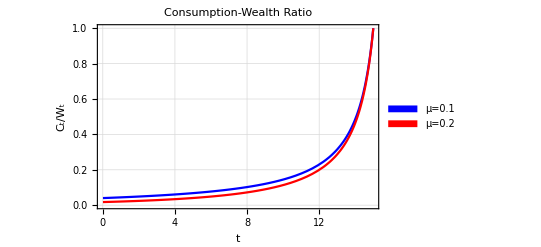

```mathematica
consumptionWealth=Plot[{optimalCW[0.1,t],optimalCW[0.2,t]},{t,0.01,15},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Wealth Ratio",
PlotLegends->Placed[SwatchLegend[{"μ=0.1","μ=0.2"}],{0.12,0.88}],
FrameLabel->{"t","C_t/W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,15},{0,Max[optimalCW[0.1,15],optimalCW[0.2,15]]}}]
Export["images/consumption-wealth-ratio-discrete-dynamic.jpeg",consumptionWealth];
```

## Pontryagin' s maximum principle

Functionals

```mathematica
yCoordinate[x_]:=√(1-x^2)
vector=Graphics3D[{Red,Arrow[{{0.7,-yCoordinate[0.7],0},{0,0,0}}]},Axes->True,Boxed->True];
sphere=SphericalPlot3D[1,{θ,0,π/2},{ϕ,0,2 π},
ImageSize->Medium,
PlotStyle->{Directive[Blue,Specularity[White,1]],Opacity[0.4]}];
vectorSphere=Show[vector,sphere,AxesLabel->{"x","y","z"},
PlotLabel->"Example of a Maximisation Problem"]
Export["images/sphere.jpeg",vectorSphere];
```

-Graphics3D-

## Dynamic Optimal Control Problem in Continuous Time

Clear variables

```mathematica
Clear["Global`*"]
```

Optimal consumption - wealth ratio

```mathematica
optimalCW[δ_,ψ_,μ_]:=ψ*δ+(1-ψ)*μ
```

Boundary conditions

```mathematica
Solve[ψ*δ+(1-ψ)*μ==0,δ]
```

{{δ→(μ (-1+ψ))/ψ}}

```mathematica
boundaryDelta[ψ_,μ_]:=(μ (-1+ψ))/ψ
```

```mathematica
Max[boundaryDelta[2,0.1],boundaryDelta[2,0.2]]
```

0.1

```mathematica
Solve[ψ*δ+(1-ψ)*μ==0,ψ]
```

{{ψ→-μ/(δ-μ)}}

```mathematica
boundaryPsi[δ_,μ_]:=-μ/(δ-μ)
```

```mathematica
Min[boundaryPsi[0.05,0.1],boundaryPsi[0.05,0.2]]
```

1.33333

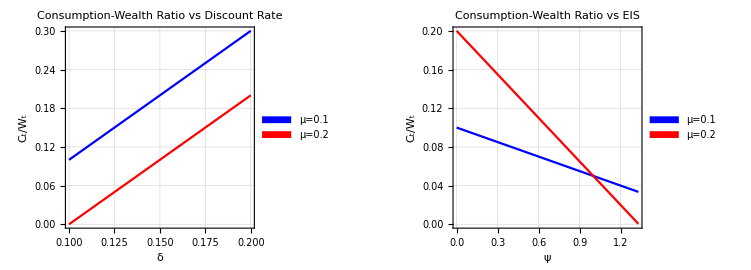

```mathematica
consumptionWealthBeta=Plot[{optimalCW[δ,2,0.1],optimalCW[δ,2,0.2]},{δ,0.1,0.2},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Wealth Ratio vs Discount Rate",
PlotLegends->Placed[SwatchLegend[{"μ=0.1","μ=0.2"}],{0.12,0.88}],
FrameLabel->{"δ","C_t/W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0.1,0.2},{0,0.3}}];
consumptionWealthPsi=Plot[{optimalCW[0.05,ψ,0.1],optimalCW[0.05,ψ,0.2]},{ψ,0,1.33},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Wealth Ratio vs EIS",
PlotLegends->Placed[SwatchLegend[{"μ=0.1","μ=0.2"}],{0.87,0.88}],
FrameLabel->{"ψ","C_t/W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,1.33},{0,0.2}}];
ConsumptionWealthRatio=GraphicsGrid[{{consumptionWealthBeta,consumptionWealthPsi}},ImageSize->{751,270}]
Export["images/consumption-wealth-ratio-continuous-dynamic.jpeg",ConsumptionWealthRatio];
```

## Solow Model

## Solow Model

Clear variables

```mathematica
Clear["Global`*"]
```

Production function

```mathematica
y[k_,l_]:=k^α*l^(1-α)
```

Parameters

```mathematica
α=0.5;
```

Plot production function

```mathematica
productionFunction=Plot3D[y[k,l],{k,0,1},{l,0,1},AxesLabel->{Subscript[K, t],Subscript[L, t],Subscript[Y, t]},ImageSize->Medium,PlotStyle->Directive[Blue,Specularity[White,1]],ViewPoint->{-5, -5, 3},PlotLabel->"Production Function"]
Export["images/production-function.jpeg",productionFunction];
```

-Graphics3D-

### Steady State Analysis

Clear variables

```mathematica
Clear["Global`*"]
```

Differential equation

```mathematica
SolowodeK[k_]:=s*k^α-(δ+n)*k
```

Plot law of motion for capital per labor

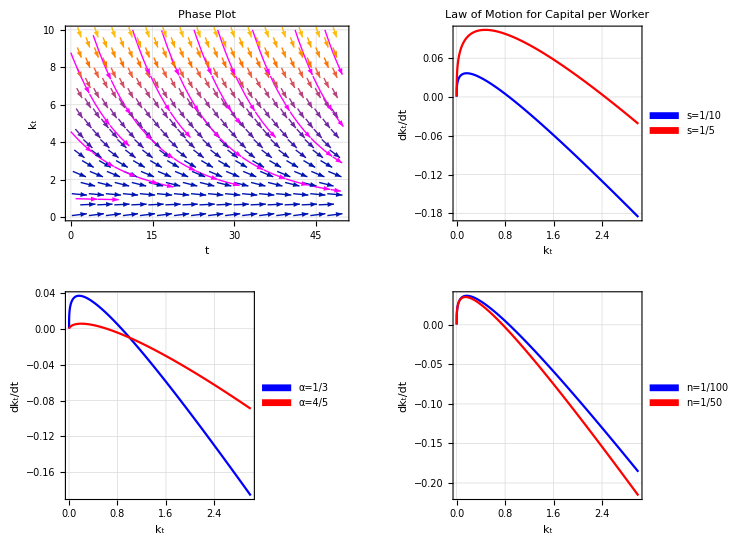

```mathematica
phasePlot=VectorPlot[{1,SolowodeK[k]//.{s->1/10,α->1/3,δ->.1,n->.01}},{t,0,50},{k,0,10},
StreamPoints->Coarse,
StreamColorFunction->None,
StreamStyle->Magenta,
PlotLabel->"Phase Plot",
FrameLabel->{"t","k_t"},
GridLines->Automatic];
odeS=Plot[Evaluate[{SolowodeK[k]//.{s->1/10,α->1/3,δ->.1,n->.01},SolowodeK[k]//.{s->2/10,α->1/3,δ->.1,n->.01}}],{k,0,3},
PlotStyle->{Blue,Red},
PlotLabel->"Law of Motion for Capital per Worker",
PlotLegends->Placed[SwatchLegend[{"s=1/10","s=1/5"}],{0.87,0.88}],
FrameLabel->{"k_t","dk_t/dt"},
Frame->True,
GridLines->Automatic];
odeA=Plot[Evaluate[{SolowodeK[k]//.{s->1/10,α->1/3,δ->.1,n->.01},SolowodeK[k]//.{s->1/10,α->4/5,δ->.1,n->.01}}],{k,0,3},
PlotStyle->{Blue,Red},
PlotLegends->Placed[SwatchLegend[{"α=1/3","α=4/5"}],{0.87,0.88}],
FrameLabel->{"k_t","dk_t/dt"},
Frame->True,
GridLines->Automatic];
odeN=Plot[Evaluate[{SolowodeK[k]//.{s->1/10,α->1/3,δ->.1,n->.01},SolowodeK[k]//.{s->1/10,α->1/3,δ->.1,n->.02}}],{k,0,3},
PlotStyle->{Blue,Red},
PlotLegends->Placed[SwatchLegend[{"n=1/100","n=1/50"}],{0.87,0.88}],
FrameLabel->{"k_t","dk_t/dt"},
Frame->True,
GridLines->Automatic];
CapitalLabor=GraphicsGrid[{{phasePlot,odeS},{odeA,odeN}},ImageSize->{751,540}]
Export["images/solow-capital-labor.jpeg",CapitalLabor];
```

Steady state

```mathematica
(s/(δ+n))^(1/(1-α))//.{s->1/10,α->1/3,δ->.1,n->.01}
```

0.866784

### Dynamic Analysis

Clear variables

```mathematica
Clear["Global`*"]
```

Solution differential equation

```mathematica
DSolve[{m'[t]==a*(1-m[t]),m[0]==m0},m[t],t]//Expand
```

{{m[t]→1-ⅇ^(-a t)+ⅇ^(-a t) m0}}

Solution of capital per output

```mathematica
m[t_,m0_]:=m0*ⅇ^(-a *t)+(1-ⅇ^(-a *t))/.a->(1-α)*( δ+n)
```

Solution of capital per worker

```mathematica
k[t_,k0_]:=(k0^(1-α) *ⅇ^(-a *t)+s/(δ+n)(1-ⅇ^(-a *t)))^(1/(1-α))/.a->(1-α)*( δ+n)
```

Plot capital per output and capital per worker

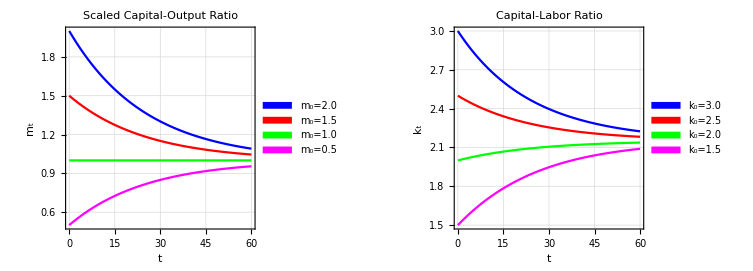

```mathematica
CapitalOutput=Plot[{m[t,2]/.{α->1/3,n->.01,δ->.05},m[t,1.5]/.{α->1/3,n->.01,δ->.05},1,m[t,0.5]/.{α->1/3,n->.01,δ->.05}},{t,0,60},
PlotStyle->{Blue,Red,Green,Magenta},
PlotLabel->"Scaled Capital-Output Ratio",
PlotLegends->Placed[SwatchLegend[{"m_0=2.0","m_0=1.5","m_0=1.0","m_0=0.5"}],{0.87,0.80}],
FrameLabel->{"t","m_t"},
Frame->True,
GridLines->Automatic];
CapitalLabor=Plot[{k[t,3]/.{α->1/3,n->.01,δ->.05,s->.1},k[t,2.5]/.{α->1/3,n->.01,δ->.05,s->.1},k[t,2]/.{α->1/3,n->.01,δ->.05,s->.1},k[t,1.5]/.{α->1/3,n->.01,δ->.05,s->.1}},{t,0,60},
PlotStyle->{Blue,Red,Green,Magenta},
PlotLabel->"Capital-Labor Ratio",
PlotLegends->Placed[SwatchLegend[{"k_0=3.0","k_0=2.5","k_0=2.0","k_0=1.5"}],{0.87,0.80}],
FrameLabel->{"t","k_t"},
Frame->True,
GridLines->Automatic];
Capital=GraphicsGrid[{{CapitalOutput,CapitalLabor}},ImageSize->{750,270}]
Export["images/solow-capital.jpeg",Capital];
```

## Ramsey Model

## Ramsey Model

Clear variables

```mathematica
Clear["Global`*"]
```

Capital

```mathematica
f[k_]:=k^0.5
```

Marginal product of capital

```mathematica
f[2.5]+{D[f[k],k]/.k->2.5}*(k-2.5)
```

{1.58114+0.316228 (-2.5+k)}

```mathematica
mpk[k_]:=1.5811388300841898+0.31622776601683794 (-2.5+k)
```

Average product of capital

```mathematica
apk[k_]:=f[2.5]/2.5*k
```

Plot capital

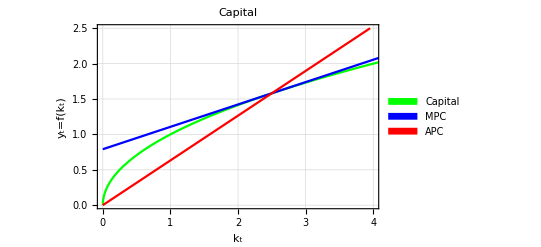

```mathematica
Capital=Plot[{f[k],mpk[k],apk[k]},{k,0,5},
PlotStyle->{Green,Blue,Red},
PlotLabel->"Capital",
PlotLegends->Placed[SwatchLegend[{"Capital","MPC","APC"}],{0.12,0.80}],
FrameLabel->{"k_t","y_t=f(k_t)"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,4},{0,2.5}}]
Export["images/ramsey-capital.jpeg",Capital];
```

## Money in the Utility Function

## Benhabib, Schmitt - Grohe & Uribe Model

Clear variables

```mathematica
Clear["Global`*"]
```

ODE for inflation with first interest rate rule

```mathematica
BenhabibOdePi[x_]:=(1-ϕ)/((1/ψ-1)*(1-θ))*(δ/ϕ+x)*x
```

Plot the ODE for inflation

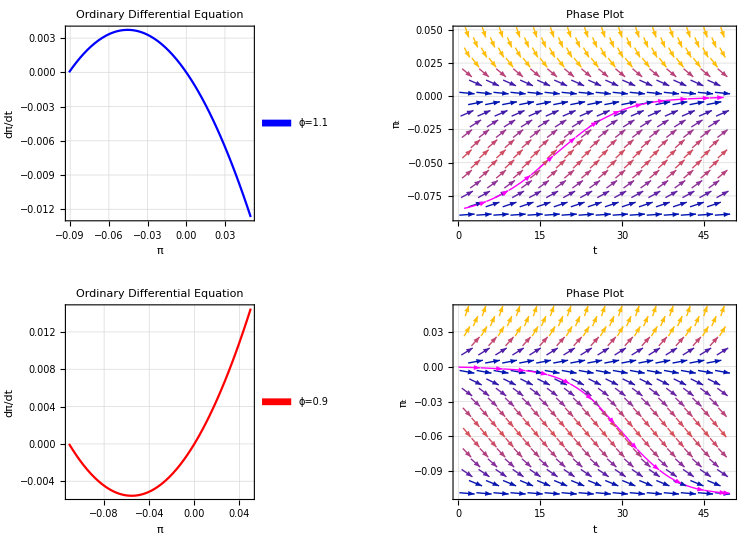

```mathematica
BenhabibOde1=Plot[{BenhabibOdePi[x]//.{ϕ->1.1,ψ->0.9,θ->0.5,δ->0.1}},{x,-0.1/1.1,0.05},
PlotStyle->{Blue},
PlotLabel->"Ordinary Differential Equation",
PlotLegends->Placed[SwatchLegend[{"ϕ=1.1"}],{0.12,0.12}],
FrameLabel->{"π","dπ/dt"},
Frame->True,
GridLines->Automatic];
BenhabibOde2=Plot[{BenhabibOdePi[x]//.{ϕ->0.9,ψ->0.9,θ->0.5,δ->0.1}},{x,-0.1/0.9,0.05},
PlotStyle->{Red},
PlotLabel->"Ordinary Differential Equation",
PlotLegends->Placed[SwatchLegend[{"ϕ=0.9"}],{0.12,0.88}],
FrameLabel->{"π","dπ/dt"},
Frame->True,
GridLines->Automatic];
phasePlot1=VectorPlot[{1,BenhabibOdePi[x]//.{ϕ->1.1,ψ->0.9,θ->0.5,δ->0.1}},{t,0,50},{x,-0.1/1.1,0.05},
StreamPoints->Coarse,
StreamColorFunction->None,
StreamStyle->Magenta,
PlotLabel->"Phase Plot",
FrameLabel->{"t","π_t"},
GridLines->Automatic];
phasePlot2=VectorPlot[{1,BenhabibOdePi[x]//.{ϕ->0.9,ψ->0.9,θ->0.5,δ->0.1}},{t,0,50},{x,-0.1/0.9,0.05},
StreamPoints->Coarse,
StreamColorFunction->None,
StreamStyle->Magenta,
PlotLabel->"Phase Plot",
FrameLabel->{"t","π_t"},
GridLines->Automatic];
Ode=GraphicsGrid[{{BenhabibOde1,phasePlot},{BenhabibOde2,phasePlot2}},ImageSize->{751,540}]
Export["images/benhabib-inflation.jpeg",Ode];
```

Difference between interest rate rules

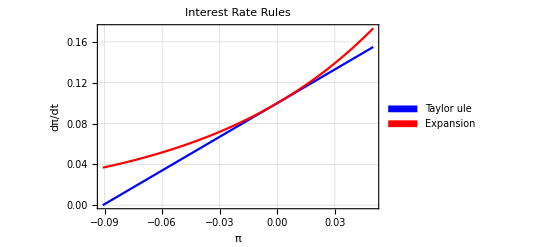

```mathematica
BenhabibRule=Plot[{δ+ϕ*x//.{ϕ->1.1,δ->0.1}, δ*ⅇ^(ϕ/δ*x)//.{ϕ->1.1,δ->0.1}},{x,-0.1/1.1,0.05},
PlotStyle->{Blue,Red},
PlotLabel->"Interest Rate Rules",
PlotLegends->Placed[SwatchLegend[{"Taylor ule","Expansion"}],{0.15,0.88}],
FrameLabel->{"π","dπ/dt"},
Frame->True,
GridLines->Automatic]
Export["images/benhabib-rule.jpeg",BenhabibRule];
```

ODE with second interest rate rule

```mathematica
BenhabibOdePi[x_]:=δ/((1/ψ-1)*(1-θ)*ϕ)*(δ+x-δ*ⅇ^(ϕ/δ*x))
```

Plot the ODE for inflation

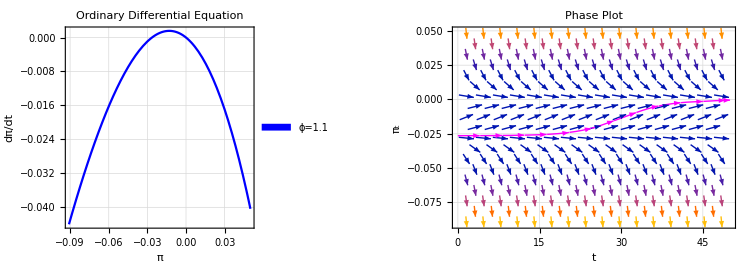

```mathematica
BenhabibOde3=Plot[{BenhabibOdePi[x]//.{ϕ->1.1,ψ->0.9,θ->0.5,δ->0.15}},{x,-0.1/1.1,0.05},
PlotStyle->{Blue},
PlotLabel->"Ordinary Differential Equation",
PlotLegends->Placed[SwatchLegend[{"ϕ=1.1"}],{0.12,0.88}],
FrameLabel->{"π","dπ/dt"},
Frame->True,
GridLines->Automatic];
phasePlot3=VectorPlot[{1,BenhabibOdePi[x]//.{ϕ->1.1,ψ->0.9,θ->0.5,δ->0.15}},{t,0,50},{x,-0.1/1.1,0.05},
StreamPoints->Coarse,
StreamColorFunction->None,
StreamStyle->Magenta,
PlotLabel->"Phase Plot",
FrameLabel->{"t","π_t"},
GridLines->Automatic];
Ode=GraphicsGrid[{{BenhabibOde3,phasePlot3}},ImageSize->{750,270}]
Export["images/benhabib-inflation-2.jpeg",Ode];
```